# Definiciones

```mathematica
sz={{1,0},{0,-1}};sp={{0,1},{0,0}};sm=Transpose[sp];sx=(sp+sm);sy=(sp-sm)/(I);s1[1]=sx;s1[2]=sy;s1[3]=sz;s1[4]={{1,0},{0,1}};s1[i_,j_]=KroneckerProduct[s1[i],s1[j]];
fs=FullSimplify;
mf=MatrixForm;
prod=KroneckerProduct;
id=IdentityMatrix;
s={sx,sy,sz};
daga=ConjugateTranspose;

(* Transpuesta parcial General *)
Clear[nu,nn,au,i,j];
ind[nu_,nn_]:={iaux=1+Floor[(nu-1)/nn],nu-(iaux-1)*nn};
rhotp[au_]:=(nn=Sqrt[Length[au]];
Table[{i,j}=ind[it,nn];{k,l}=ind[jt,nn];
au[[nn*(i-1)+l,nn*(k-1)+j]],{it,nn^2},{jt,nn^2}]); 

(* Base Estándar *)

st0={1,0};st1={0,1};
st00=Flatten[prod[st0,st0]];
st01=Flatten[prod[st0,st1]];
st10=Flatten[prod[st1,st0]];
st11=Flatten[prod[st1,st1]];

(* Proyectores en la Base Estándar *)

P0={{1,0},{0,0}};
P1={{0,0},{0,1}};

n[1]={1,0,0}; n[2]={0,1,0};n[3]={0,0,1};n[4]={1,0,1}/Sqrt[2];
σ={s1[1],s1[2],s1[3]};

(* Rotación General de un qubit *)

R[i_,θ_]=MatrixExp[-I θ n[i].σ/2] ;
```

Código para hacer traza parcial

```mathematica
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])
```

```mathematica
eps=10^-10.
```

1.×10^-10

```mathematica
(* Estado GHZ *)
```

```mathematica
Psi0=(Flatten[prod[st0,st0,st0]]+Flatten[prod[st1,st1,st1]])/√2
```

{1/(√2),0,0,0,0,0,0,1/(√2)}

```mathematica
Psi0.Psi0
```

1

```mathematica
rho0ABT=prod[Psi0,Psi0]
```

{{1/2,0,0,0,0,0,0,1/2},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1/2,0,0,0,0,0,0,1/2}}

```mathematica
(* Medir t en la base standard *)
```

```mathematica
M0=prod[s1[4],s1[4],P0]
```

{{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0}}

```mathematica
M1=prod[s1[4],s1[4],P1]
```

{{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1}}

```mathematica
rho0ABTprima=M0.rho0ABT.M0+M1.rho0ABT.M1
```

{{1/2,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1/2}}

```mathematica
rho0ATprima=TraceSystem[rho0ABTprima,{2}]
```

{{1/2,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1/2}}

```mathematica
(* Información Mutua IAT=SrhoA+SrhoT-SrhoAT *)
```

```mathematica
rho0Aprima=TraceSystem[rho0ATprima,{2}]
```

{{1/2,0},{0,1/2}}

```mathematica
rho0Tprima=TraceSystem[rho0ATprima,{1}]
```

{{1/2,0},{0,1/2}}

```mathematica
λrho0ATprima=Eigenvalues[rho0ATprima]//Chop
```

{1/2,1/2,0,0}

```mathematica
λrho0Aprima=Eigenvalues[rho0Aprima]//Chop
λrho0Tprima=Eigenvalues[rho0Tprima]//Chop
{0.5,0.5}
{0.5,0.5}
```

{1/2,1/2}

{1/2,1/2}

{0.5,0.5}

{0.5,0.5}

```mathematica
Srho0Aprima=-Sum[λrho0Aprima[[i]]Log2[eps+λrho0Aprima[[i]]],{i,1,2}]


Srho0Tprima=-Sum[λrho0Tprima[[i]]Log2[λrho0Tprima[[i]]],{i,1,2}]
```

1.

1

```mathematica
λrho0ATprima
```

{1/2,1/2,0,0}

```mathematica
Log2[0]
```

-∞

```mathematica
Srho0ATprima=-Sum[λrho0ATprima[[i]]Log2[ λrho0ATprima[[i]]],{i,1,2}]
```

1

```mathematica
ep=0.000001;
```

```mathematica
Srho0ATprima=-Sum[ep+λrho0ATprima[[i]]Log2[ep + λrho0ATprima[[i]]],{i,1,4}]
```

0.999993

```mathematica
(* Información Mutua IAT=SrhoA+SrhoT-SrhoAT *)
```

```mathematica
IATprima=1+1-1
```

1

```mathematica
Clear[th];
```

```mathematica
(* Si ahora se cambia de baste en A, |0> --> Cos[th/2]-Sin[th/2] |1> --> Cos[th/2]+Sin[th/2] *)
```

```mathematica
st0p=Cos[th/2]st0-Sin[th/2]st1
st1p=Cos[th/2]st0+Sin[th/2]st1
```

{Cos[th/2],-Sin[th/2]}

{Cos[th/2],Sin[th/2]}

```mathematica
Psi1=(Flatten[prod[st0p,st0,st0]]+Flatten[prod[st1p,st1,st1]])/√2
```

{Cos[th/2]/(√2),0,0,Cos[th/2]/(√2),-Sin[th/2]/(√2),0,0,Sin[th/2]/(√2)}

```mathematica
rho1ABT=prod[Psi1,Psi1]
```

{{1/2 Cos[th/2]^2,0,0,1/2 Cos[th/2]^2,-1/2 Cos[th/2] Sin[th/2],0,0,1/2 Cos[th/2] Sin[th/2]},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1/2 Cos[th/2]^2,0,0,1/2 Cos[th/2]^2,-1/2 Cos[th/2] Sin[th/2],0,0,1/2 Cos[th/2] Sin[th/2]},{-1/2 Cos[th/2] Sin[th/2],0,0,-1/2 Cos[th/2] Sin[th/2],1/2 Sin[th/2]^2,0,0,-1/2 Sin[th/2]^2},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1/2 Cos[th/2] Sin[th/2],0,0,1/2 Cos[th/2] Sin[th/2],-1/2 Sin[th/2]^2,0,0,1/2 Sin[th/2]^2}}

```mathematica
rho1ABTprima=M0.rho1ABT.M0+M1.rho1ABT.M1
```

{{1/2 Cos[th/2]^2,0,0,0,-1/2 Cos[th/2] Sin[th/2],0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,1/2 Cos[th/2]^2,0,0,0,1/2 Cos[th/2] Sin[th/2]},{-1/2 Cos[th/2] Sin[th/2],0,0,0,1/2 Sin[th/2]^2,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,1/2 Cos[th/2] Sin[th/2],0,0,0,1/2 Sin[th/2]^2}}

```mathematica
(* Estado rhoAT traceando el sistema B *)
```

```mathematica
rho1ATprima=TraceSystem[rho1ABTprima,{2}]
```

{{1/2 Cos[th/2]^2,0,-1/2 Cos[th/2] Sin[th/2],0},{0,1/2 Cos[th/2]^2,0,1/2 Cos[th/2] Sin[th/2]},{-1/2 Cos[th/2] Sin[th/2],0,1/2 Sin[th/2]^2,0},{0,1/2 Cos[th/2] Sin[th/2],0,1/2 Sin[th/2]^2}}

```mathematica
rho1Aprima=TraceSystem[rho1ATprima,{2}]
```

{{Cos[th/2]^2,0},{0,Sin[th/2]^2}}

```mathematica
(* Estado rhoT traceando a su vez el sistema T *)
```

```mathematica
rho1Tprima=TraceSystem[rho1ATprima,{1}]//FullSimplify
```

{{1/2,0},{0,1/2}}

```mathematica
(* Autovalores y entropías de Von Neumann *)

λrho1Aprima=Eigenvalues[rho1Aprima]//Chop
λrho1Tprima=Eigenvalues[rho1Tprima]//Chop


Srho1Aprima=-Sum[λrho1Aprima[[i]]Log2[λrho1Aprima[[i]]],{i,1,2}]
Srho1Tprima=-Sum[λrho0Tprima[[i]]Log2[λrho1Tprima[[i]]],{i,1,2}]
```

{Cos[th/2]^2,Sin[th/2]^2}

{1/2,1/2}

-(Cos[th/2]^2 Log[Cos[th/2]^2])/Log[2]-(Log[Sin[th/2]^2] Sin[th/2]^2)/Log[2]

1

```mathematica
λrho1ATprima=Eigenvalues[rho1ATprima]
```

{1/2,1/2,0,0}

```mathematica
ep=0.00000000001;
```

```mathematica
Srho1ATprima=-Sum[ep+λrho1ATprima[[i]]Log2[ep + λrho1ATprima[[i]]],{i,1,4}]
```

0.999993

```mathematica
IAT1prima=Srho1Aprima+Srho1Tprima-1
```

-(Cos[th/2]^2 Log[Cos[th/2]^2])/Log[2]-(Log[Sin[th/2]^2] Sin[th/2]^2)/Log[2]

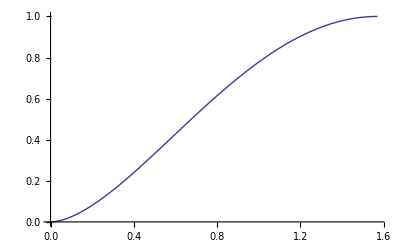

```mathematica
Plot[IAT1prima,{th,0,Pi/2}]
```

```mathematica
(* Medida Proyectiva con un ángulo alfa *)
```

```mathematica
Clear[al];
```

```mathematica
Clear[M0al,M1al];
```

```mathematica
st0al=Sin[al/2]st0-Cos[al/2]st1;
st1al=Cos[al/2]st0+Sin[al/2]st1;
```

```mathematica
st0al.st1al//FullSimplify
```

0

```mathematica
st0al
```

{1/(√2),-1/(√2)}

```mathematica
Clear[al];

al=.;

st0al=Sin[al/2]st0-Cos[al/2]st1;
st1al=Cos[al/2]st0+Sin[al/2]st1;
```

```mathematica
st1al.st1al
```

Cos[al/2]^2+Sin[al/2]^2

```mathematica
st0al.st1al
```

0

```mathematica
Pal0=prod[st0al,st0al]
```

{{Sin[al/2]^2,-Cos[al/2] Sin[al/2]},{-Cos[al/2] Sin[al/2],Cos[al/2]^2}}

```mathematica
Pal1=prod[st1al,st1al]
```

{{Cos[al/2]^2,Cos[al/2] Sin[al/2]},{Cos[al/2] Sin[al/2],Sin[al/2]^2}}

```mathematica
al=Pi;
```

```mathematica
Pal1
```

{{0,0},{0,1}}

```mathematica
MM0al=prod[s1[4],s1[4],Pal0]
```

{{Sin[al/2]^2,-Cos[al/2] Sin[al/2],0,0,0,0,0,0},{-Cos[al/2] Sin[al/2],Cos[al/2]^2,0,0,0,0,0,0},{0,0,Sin[al/2]^2,-Cos[al/2] Sin[al/2],0,0,0,0},{0,0,-Cos[al/2] Sin[al/2],Cos[al/2]^2,0,0,0,0},{0,0,0,0,Sin[al/2]^2,-Cos[al/2] Sin[al/2],0,0},{0,0,0,0,-Cos[al/2] Sin[al/2],Cos[al/2]^2,0,0},{0,0,0,0,0,0,Sin[al/2]^2,-Cos[al/2] Sin[al/2]},{0,0,0,0,0,0,-Cos[al/2] Sin[al/2],Cos[al/2]^2}}

```mathematica
MM1al=prod[s1[4],s1[4],Pal1]
```

{{Cos[al/2]^2,Cos[al/2] Sin[al/2],0,0,0,0,0,0},{Cos[al/2] Sin[al/2],Sin[al/2]^2,0,0,0,0,0,0},{0,0,Cos[al/2]^2,Cos[al/2] Sin[al/2],0,0,0,0},{0,0,Cos[al/2] Sin[al/2],Sin[al/2]^2,0,0,0,0},{0,0,0,0,Cos[al/2]^2,Cos[al/2] Sin[al/2],0,0},{0,0,0,0,Cos[al/2] Sin[al/2],Sin[al/2]^2,0,0},{0,0,0,0,0,0,Cos[al/2]^2,Cos[al/2] Sin[al/2]},{0,0,0,0,0,0,Cos[al/2] Sin[al/2],Sin[al/2]^2}}

```mathematica
MM0al.MM0al+MM1al.MM1al//FullSimplify
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
rho1ABT
```

{{1/2 Cos[th/2]^2,0,0,1/2 Cos[th/2]^2,-1/2 Cos[th/2] Sin[th/2],0,0,1/2 Cos[th/2] Sin[th/2]},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1/2 Cos[th/2]^2,0,0,1/2 Cos[th/2]^2,-1/2 Cos[th/2] Sin[th/2],0,0,1/2 Cos[th/2] Sin[th/2]},{-1/2 Cos[th/2] Sin[th/2],0,0,-1/2 Cos[th/2] Sin[th/2],1/2 Sin[th/2]^2,0,0,-1/2 Sin[th/2]^2},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1/2 Cos[th/2] Sin[th/2],0,0,1/2 Cos[th/2] Sin[th/2],-1/2 Sin[th/2]^2,0,0,1/2 Sin[th/2]^2}}

```mathematica
rho1ABTprima //FullSimplify
```

{{1/4 (1+Cos[th]),0,0,0,-Sin[th]/4,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,1/4 (1+Cos[th]),0,0,0,Sin[th]/4},{-Sin[th]/4,0,0,0,1/4 (1-Cos[th]),0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,Sin[th]/4,0,0,0,1/4 (1-Cos[th])}}

```mathematica
rho1ABTalprima=MM0al.rho1ABT.MM0al+MM1al.rho1ABT.MM1al//FullSimplify
```

{{1/8 (3+Cos[2 al]) Cos[th/2]^2,1/4 Cos[al] Cos[th/2]^2 Sin[al],1/4 Cos[al] Cos[th/2]^2 Sin[al],1/4 Cos[th/2]^2 Sin[al]^2,-1/16 (3+Cos[2 al]) Sin[th],-1/8 Cos[al] Sin[al] Sin[th],1/8 Cos[al] Sin[al] Sin[th],1/8 Sin[al]^2 Sin[th]},{1/4 Cos[al] Cos[th/2]^2 Sin[al],1/4 Cos[th/2]^2 Sin[al]^2,1/4 Cos[th/2]^2 Sin[al]^2,-1/4 Cos[al] Cos[th/2]^2 Sin[al],-1/8 Cos[al] Sin[al] Sin[th],-1/8 Sin[al]^2 Sin[th],1/8 Sin[al]^2 Sin[th],-1/8 Cos[al] Sin[al] Sin[th]},{1/4 Cos[al] Cos[th/2]^2 Sin[al],1/4 Cos[th/2]^2 Sin[al]^2,1/4 Cos[th/2]^2 Sin[al]^2,-1/4 Cos[al] Cos[th/2]^2 Sin[al],-1/8 Cos[al] Sin[al] Sin[th],-1/8 Sin[al]^2 Sin[th],1/8 Sin[al]^2 Sin[th],-1/8 Cos[al] Sin[al] Sin[th]},{1/4 Cos[th/2]^2 Sin[al]^2,-1/4 Cos[al] Cos[th/2]^2 Sin[al],-1/4 Cos[al] Cos[th/2]^2 Sin[al],1/8 (3+Cos[2 al]) Cos[th/2]^2,-1/8 Sin[al]^2 Sin[th],1/8 Cos[al] Sin[al] Sin[th],-1/8 Cos[al] Sin[al] Sin[th],1/16 (3+Cos[2 al]) Sin[th]},{-1/16 (3+Cos[2 al]) Sin[th],-1/8 Cos[al] Sin[al] Sin[th],-1/8 Cos[al] Sin[al] Sin[th],-1/8 Sin[al]^2 Sin[th],1/8 (3+Cos[2 al]) Sin[th/2]^2,1/4 (Cos[al/2]+Cos[(3 al)/2]) Sin[al/2] Sin[th/2]^2,1/8 Cos[al] (-1+Cos[th]) Sin[al],-1/4 Sin[al]^2 Sin[th/2]^2},{-1/8 Cos[al] Sin[al] Sin[th],-1/8 Sin[al]^2 Sin[th],-1/8 Sin[al]^2 Sin[th],1/8 Cos[al] Sin[al] Sin[th],1/4 (Cos[al/2]+Cos[(3 al)/2]) Sin[al/2] Sin[th/2]^2,1/4 Sin[al]^2 Sin[th/2]^2,-1/4 Sin[al]^2 Sin[th/2]^2,1/4 (Cos[al/2]+Cos[(3 al)/2]) Sin[al/2] Sin[th/2]^2},{1/8 Cos[al] Sin[al] Sin[th],1/8 Sin[al]^2 Sin[th],1/8 Sin[al]^2 Sin[th],-1/8 Cos[al] Sin[al] Sin[th],1/8 Cos[al] (-1+Cos[th]) Sin[al],-1/4 Sin[al]^2 Sin[th/2]^2,1/4 Sin[al]^2 Sin[th/2]^2,1/8 Cos[al] (-1+Cos[th]) Sin[al]},{1/8 Sin[al]^2 Sin[th],-1/8 Cos[al] Sin[al] Sin[th],-1/8 Cos[al] Sin[al] Sin[th],1/16 (3+Cos[2 al]) Sin[th],-1/4 Sin[al]^2 Sin[th/2]^2,1/4 (Cos[al/2]+Cos[(3 al)/2]) Sin[al/2] Sin[th/2]^2,1/8 Cos[al] (-1+Cos[th]) Sin[al],1/8 (3+Cos[2 al]) Sin[th/2]^2}}

```mathematica
Tr[rho1ABTalprima]//FullSimplify
```

1

```mathematica
rho1ATalprima=TraceSystem[rho1ABTalprima,{2}]//FullSimplify
```

{{1/4 (1+Cos[th]),0,-1/4 Cos[al]^2 Sin[th],-1/4 Cos[al] Sin[al] Sin[th]},{0,1/4 (1+Cos[th]),-1/4 Cos[al] Sin[al] Sin[th],1/4 Cos[al]^2 Sin[th]},{-1/4 Cos[al]^2 Sin[th],-1/4 Cos[al] Sin[al] Sin[th],1/4 (1-Cos[th]),0},{-1/4 Cos[al] Sin[al] Sin[th],1/4 Cos[al]^2 Sin[th],0,1/4 (1-Cos[th])}}

```mathematica
TraceSystem[rho1ABTalprima,{2,3}]//FullSimplify
```

{{Cos[th/2]^2,0},{0,Sin[th/2]^2}}

```mathematica
rho1Aalprima=TraceSystem[rho1ATalprima,{2}]//FullSimplify
```

{{Cos[th/2]^2,0},{0,Sin[th/2]^2}}

```mathematica
TraceSystem[rho1ABTalprima,{1,2}]//FullSimplify
```

{{1/2,0},{0,1/2}}

```mathematica
rho1Talprima=TraceSystem[rho1ATalprima,{1}]//FullSimplify
```

{{1/2,0},{0,1/2}}

```mathematica
λrho1alAprima=Eigenvalues[rho1Aalprima]//Chop
λrho1alTprima=Eigenvalues[rho1Talprima]//Chop
```

{Cos[th/2]^2,Sin[th/2]^2}

{1/2,1/2}

```mathematica
Clear[al,th];rho1ATalprima//MatrixForm//FullSimplify
```

(1/4 (1+Cos[th]) | 0 | -1/4 Cos[al]^2 Sin[th] | -1/4 Cos[al] Sin[al] Sin[th]
0 | 1/4 (1+Cos[th]) | -1/4 Cos[al] Sin[al] Sin[th] | 1/4 Cos[al]^2 Sin[th]
-1/4 Cos[al]^2 Sin[th] | -1/4 Cos[al] Sin[al] Sin[th] | 1/4 (1-Cos[th]) | 0
-1/4 Cos[al] Sin[al] Sin[th] | 1/4 Cos[al]^2 Sin[th] | 0 | 1/4 (1-Cos[th]))

```mathematica
rATalprima=({{1/2 c^2, 0, -1/4 ca^2 *s1, -1/8 s2 *s1}, {0, 1/2 c^2, -1/8 s2 *s1, 1/4 ca^2 *s1}, {-1/4 ca^2 *s1, -1/8 s2 *s1, 1/2 s^2, 0}, {-1/8 s2 *s1, 1/4 ca^2 *s1, 0, 1/2 s^2}})
```

```mathematica
(** c=Cos(th/2) s=Sin(th/2) ca=Cos(al) s1=Sin(th) s2=Sin(2 al)  1/4 ca^2 *s1=Aa;-1/8 s2 *s1=Bb;1/4 ca^2 *s1=Cc; *))
```

Set::write: Tag Times in (ca^2 s1)/4 is Protected.

Set::write: Tag Times in -(s1 s2)/8 is Protected.

Set::write: Tag Times in (ca^2 s1)/4 is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

```mathematica
Clear[c,s,ca];


rATalprimaM=({{1/2 c^2, 0, -Aa, Bb}, {0, 1/2 c^2, Bb, Aa}, {-Aa, Bb, 1/2 s^2, 0}, {Bb, Aa, 0, 1/2 s^2}})
```

{{c^2/2,0,-Aa,Bb},{0,c^2/2,Bb,Aa},{-Aa,Bb,s^2/2,0},{Bb,Aa,0,s^2/2}}

```mathematica
?Assuming
```

Assuming[assum,expr] evaluates expr with assum appended to $Assumptions, so that assum is included in the default assumptions used by functions such as Refine, Simplify and Integrate.

```mathematica
Eigenvalues[rATalprimaM]
```

{1/4 (c^2+s^2-√(16 Aa^2+16 Bb^2+c^4-2 c^2 s^2+s^4)),1/4 (c^2+s^2-√(16 Aa^2+16 Bb^2+c^4-2 c^2 s^2+s^4)),1/4 (c^2+s^2+√(16 Aa^2+16 Bb^2+c^4-2 c^2 s^2+s^4)),1/4 (c^2+s^2+√(16 Aa^2+16 Bb^2+c^4-2 c^2 s^2+s^4))}

```mathematica
√(16 (1/4 ca^2 *s1)^2+16 (-1/8 s2 *s1)^2+c^4-2 c^2 s^2+s^4)//FullSimplify
```

√((c^2-s^2)^2+1/4 s1^2 (4 ca^4+s2^2))

```mathematica
√((Cos[th/2]^2-Sin[th/2]^2)^2+1/4 Sin[th]^2 (4 Cos[al]^4+Sin[2*al]^2))
```

```mathematica
√((Cos[th/2]^2-Sin[th/2]^2)^2+1/4 (4 Cos[al]^4+Sin[2 al]^2) Sin[th]^2)//FullSimplify
```

1/2 √(3+Cos[2 al]+2 Cos[2 th] Sin[al]^2)

```mathematica
lamda={1/4 (1-1/2 √(3+Cos[2 al]+2 Cos[2 th] Sin[al]^2)),1/4  (1-1/2 √(3+Cos[2 al]+2 Cos[2 th] Sin[al]^2)),1/4  (1+1/2 √(3+Cos[2 al]+2 Cos[2 th] Sin[al]^2)),1/4  (1+1/2 √(3+Cos[2 al]+2 Cos[2 th] Sin[al]^2))}//FullSimplify
```

{1/8 (2-√(3+Cos[2 al]+2 Cos[2 th] Sin[al]^2)),1/8 (2-√(3+Cos[2 al]+2 Cos[2 th] Sin[al]^2)),1/8 (2+√(3+Cos[2 al]+2 Cos[2 th] Sin[al]^2)),1/8 (2+√(3+Cos[2 al]+2 Cos[2 th] Sin[al]^2))}

```mathematica
Clear[c,s,ca];
Assuming[c^2+s^2=1,Eigenvalues[rATalprima] ]
```

Set::write: Tag Plus in c^2 + s^2 is Protected.

$Assumptions::bass: 1 is not a well-formed assumption.

{1/8 (2 c^2+2 s^2-√(4 c^4-8 c^2 s^2+4 s^4+4 ca^4 s1^2+s1^2 s2^2)),1/8 (2 c^2+2 s^2-√(4 c^4-8 c^2 s^2+4 s^4+4 ca^4 s1^2+s1^2 s2^2)),1/8 (2 c^2+2 s^2+√(4 c^4-8 c^2 s^2+4 s^4+4 ca^4 s1^2+s1^2 s2^2)),1/8 (2 c^2+2 s^2+√(4 c^4-8 c^2 s^2+4 s^4+4 ca^4 s1^2+s1^2 s2^2))}

```mathematica
eig={1/8 (2-√(4 -8 c^2 s^2+4 ca^4 s1^2+s1^2 s2^2)),1/8 (2 -√(4 -8 c^2 s^2+4 ca^4 s1^2+s1^2 s2^2)),1/8 (2 +√(4 -8 c^2 s^2+4 ca^4 s1^2+s1^2 s2^2)),1/8 (2 +√(4 -8 c^2 s^2+4 ca^4 s1^2+s1^2 s2^2))}
```

{1/8 (2-√(4-8 c^2 s^2+4 ca^4 s1^2+s1^2 s2^2)),1/8 (2-√(4-8 c^2 s^2+4 ca^4 s1^2+s1^2 s2^2)),1/8 (2+√(4-8 c^2 s^2+4 ca^4 s1^2+s1^2 s2^2)),1/8 (2+√(4-8 c^2 s^2+4 ca^4 s1^2+s1^2 s2^2))}

```mathematica
(*c y s son de th y s2= sen(2*alpha) y ca=cos[alpha]*)
rho1alAprima
```

{{Cos[th/2]^2,0},{0,Sin[th/2]^2}}

```mathematica
λrho1alATprima=Eigenvalues[rho1ATalprima]//FullSimplify
```

{1/8 (2-√(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2)),1/8 (2-√(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2)),1/8 (2+√(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2)),1/8 (2+√(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2))}

```mathematica
Srhoal1Aprima=-Sum[eps+λrho1alAprima[[i]]Log2[eps+λrho1alAprima[[i]]],{i,1,2}]//Chop
```

-2.×10^-10-(Cos[th/2]^2 Log[1.×10^-10+Cos[th/2]^2])/Log[2]-(Log[1.×10^-10+Sin[th/2]^2] Sin[th/2]^2)/Log[2]

```mathematica
Srho1alTprima=-Sum[eps+λrho1alTprima[[i]]Log2[eps+λrho1alTprima[[i]]],{i,1,2}]
```

1.

```mathematica
Srho1alATprima=-Sum[eps+λrho1alATprima[[i]]Log2[eps + λrho1alATprima[[i]]],{i,1,4}]//Chop//FullSimplify
```

-4.×10^-10+0.360674 Log[0.25-0.125 √(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2)] (-2.+√(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2))-0.360674 Log[0.125 (2.+√(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2))] (2+√(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2))

```mathematica
Srhoal1Aprima
```

-2.×10^-10-(Cos[th/2]^2 Log[1.×10^-10+Cos[th/2]^2])/Log[2]-(Log[1.×10^-10+Sin[th/2]^2] Sin[th/2]^2)/Log[2]

```mathematica
IATal1prima=Srhoal1Aprima+1-Srho1alATprima
```

1.-(Cos[th/2]^2 Log[1.×10^-10+Cos[th/2]^2])/Log[2]-(Log[1.×10^-10+Sin[th/2]^2] Sin[th/2]^2)/Log[2]-0.360674 Log[0.25-0.125 √(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2)] (-2.+√(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2))+0.360674 Log[0.125 (2.+√(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2))] (2+√(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2))

```mathematica
P1al
```

{{0,0},{0,1}}

```mathematica
al=.;th=.;
```

```mathematica
IATal1prima
```

1.-(Cos[th/2]^2 Log[1.×10^-10+Cos[th/2]^2])/Log[2]-(Log[1.×10^-10+Sin[th/2]^2] Sin[th/2]^2)/Log[2]-0.360674 Log[0.25-0.125 √(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2)] (-2.+√(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2))+0.360674 Log[0.125 (2.+√(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2))] (2+√(3+Cos[2 th]+2 Cos[2 al] Sin[th]^2))

```mathematica
Plot[IATal1prima,{th,0,Pi/2}]
```

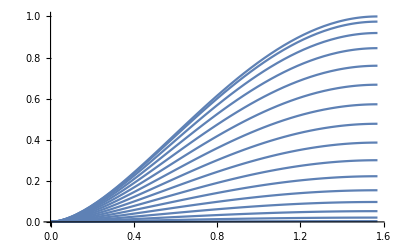

```mathematica
Plot[Table[al=all;IATal1prima,{all,0,Pi/2,0.1}],{th,0,Pi/2}]
```

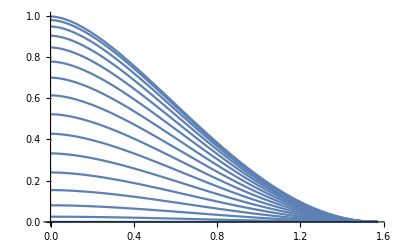

```mathematica
Plot[Table[th=thh;IATal1prima,{thh,0,Pi/2,0.1}],{al,0,Pi/2}]
```

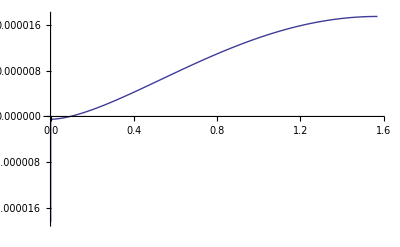

```mathematica
Plot[IATal1prima,{th,0,Pi/2}]
```

```mathematica
Clear[al];
Table[al=all;{all,th,IATal1prima},{all,0,Pi/2,0.5},{th,0,Pi/2,0.1}]



-(Cos[th/2]^2 Log[Cos[th/2]^2])/Log[2]-(Log[Sin[th/2]^2] Sin[th/2]^2)/Log[2]
1
```

{{{0.,0.,Indeterminate},{0.,0.1,Indeterminate},{0.,0.2,Indeterminate},{0.,0.3,Indeterminate},{0.,0.4,Indeterminate},{0.,0.5,Indeterminate},{0.,0.6,Indeterminate},{0.,0.7,Indeterminate},{0.,0.8,Indeterminate},{0.,0.9,Indeterminate},{0.,1.,Indeterminate},{0.,1.1,Indeterminate},{0.,1.2,Indeterminate},{0.,1.3,Indeterminate},{0.,1.4,Indeterminate},{0.,1.5,Indeterminate}},{{0.5,0.,Indeterminate},{0.5,0.1,0.0136382},{0.5,0.2,0.0427033},{0.5,0.3,0.0804986},{0.5,0.4,0.123467},{0.5,0.5,0.169128},{0.5,0.6,0.215581},{0.5,0.7,0.261289},{0.5,0.8,0.30498},{0.5,0.9,0.345585},{0.5,1.,0.382203},{0.5,1.1,0.414084},{0.5,1.2,0.44061},{0.5,1.3,0.461289},{0.5,1.4,0.475751},{0.5,1.5,0.483742}},{{1.,0.,Indeterminate},{1.,0.1,0.00185686},{1.,0.2,0.00574209},{1.,0.3,0.0107253},{1.,0.4,0.0163311},{1.,0.5,0.0222389},{1.,0.6,0.0282089},{1.,0.7,0.0340513},{1.,0.8,0.0396111},{1.,0.9,0.0447596},{1.,1.,0.0493891},{1.,1.1,0.0534102},{1.,1.2,0.0567498},{1.,1.3,0.0593496},{1.,1.4,0.061166},{1.,1.5,0.062169}},{{1.5,0.,Indeterminate},{1.5,0.1,5.32726×10^-8},{1.5,0.2,1.18382×10^-6},{1.5,0.3,2.63122×10^-6},{1.5,0.4,4.25726×10^-6},{1.5,0.5,5.96909×10^-6},{1.5,0.6,7.69748×10^-6},{1.5,0.7,9.38782×10^-6},{1.5,0.8,0.0000109955},{1.5,0.9,0.0000124836},{1.5,1.,0.0000138213},{1.5,1.1,0.0000149828},{1.5,1.2,0.0000159473},{1.5,1.3,0.000016698},{1.5,1.4,0.0000172224},{1.5,1.5,0.000017512}}}

-(Cos[th/2]^2 Log[Cos[th/2]^2])/Log[2]-(Log[Sin[th/2]^2] Sin[th/2]^2)/Log[2]

1

```mathematica
al=0;Plot[Table[al=all;IAT1alprima,{all,0,Pi/2,0.1}],{th,0,Pi/2}]
```

{{1/2,0},{0,1/2}}

{{1/2,0},{0,1/2}}

{Cos[th/2]^2,Sin[th/2]^2}

{1/2,1/2}

-(Cos[th/2]^2 Log[Cos[th/2]^2])/Log[2]-(Log[Sin[th/2]^2] Sin[th/2]^2)/Log[2]

1

{Cos[th/2]^2,Sin[th/2]^2}

{1/2,1/2}

-(Cos[th/2]^2 Log[Cos[th/2]^2])/Log[2]-(Log[Sin[th/2]^2] Sin[th/2]^2)/Log[2]

1

{1/2,1/2,0,0}

{1/2,1/2,0,0}

1.

1.

-(Cos[th/2]^2 Log[Cos[th/2]^2])/Log[2]-(Log[Sin[th/2]^2] Sin[th/2]^2)/Log[2]

-(Cos[th/2]^2 Log[Cos[th/2]^2])/Log[2]-(Log[Sin[th/2]^2] Sin[th/2]^2)/Log[2]

```mathematica
Medida Generalizada
```

```mathematica
M2al=



P0al=prod[st0al,st0al];P1al=prod[st1al,st1al];

P0al=prod[st0al,st0al]
{{Cos[al/2]^2,-Cos[al/2] Sin[al/2]},{-Cos[al/2] Sin[al/2],Sin[al/2]^2}}

M0al.M0al
{{Cos[al/2]^4+Sin[al]^2/4,-1/2 Cos[al/2]^2 Sin[al]-1/2 Sin[al/2]^2 Sin[al],0,0,0,0,0,0},{-1/2 Cos[al/2]^2 Sin[al]-1/2 Sin[al/2]^2 Sin[al],Sin[al/2]^4+Sin[al]^2/4,0,0,0,0,0,0},{0,0,Cos[al/2]^4+Sin[al]^2/4,-1/2 Cos[al/2]^2 Sin[al]-1/2 Sin[al/2]^2 Sin[al],0,0,0,0},{0,0,-1/2 Cos[al/2]^2 Sin[al]-1/2 Sin[al/2]^2 Sin[al],Sin[al/2]^4+Sin[al]^2/4,0,0,0,0},{0,0,0,0,Cos[al/2]^4+Sin[al]^2/4,-1/2 Cos[al/2]^2 Sin[al]-1/2 Sin[al/2]^2 Sin[al],0,0},{0,0,0,0,-1/2 Cos[al/2]^2 Sin[al]-1/2 Sin[al/2]^2 Sin[al],Sin[al/2]^4+Sin[al]^2/4,0,0},{0,0,0,0,0,0,Cos[al/2]^4+Sin[al]^2/4,-1/2 Cos[al/2]^2 Sin[al]-1/2 Sin[al/2]^2 Sin[al]},{0,0,0,0,0,0,-1/2 Cos[al/2]^2 Sin[al]-1/2 Sin[al/2]^2 Sin[al],Sin[al/2]^4+Sin[al]^2/4}}

prod[s1[4],s1[4],P0al]//FullSimplify //MatrixForm
({{Cos[al/2]^2, -Sin[al]/2, 0, 0, 0, 0, 0, 0}, {-Sin[al]/2, Sin[al/2]^2, 0, 0, 0, 0, 0, 0}, {0, 0, Cos[al/2]^2, -Sin[al]/2, 0, 0, 0, 0}, {0, 0, -Sin[al]/2, Sin[al/2]^2, 0, 0, 0, 0}, {0, 0, 0, 0, Cos[al/2]^2, -Sin[al]/2, 0, 0}, {0, 0, 0, 0, -Sin[al]/2, Sin[al/2]^2, 0, 0}, {0, 0, 0, 0, 0, 0, Cos[al/2]^2, -Sin[al]/2}, {0, 0, 0, 0, 0, 0, -Sin[al]/2, Sin[al/2]^2}})

Tr[prod[s1[4],s1[4],P0al].prod[s1[4],s1[4],P0al]]//FullSimplify
4

Tr[M0al.M0al]//FullSimplify
4

Transpose[prod[s1[4],s1[4],P1al]]//FullSimplify//MatrixForm
({{Cos[al/2]^2, Sin[al]/2, 0, 0, 0, 0, 0, 0}, {Sin[al]/2, Sin[al/2]^2, 0, 0, 0, 0, 0, 0}, {0, 0, Cos[al/2]^2, Sin[al]/2, 0, 0, 0, 0}, {0, 0, Sin[al]/2, Sin[al/2]^2, 0, 0, 0, 0}, {0, 0, 0, 0, Cos[al/2]^2, Sin[al]/2, 0, 0}, {0, 0, 0, 0, Sin[al]/2, Sin[al/2]^2, 0, 0}, {0, 0, 0, 0, 0, 0, Cos[al/2]^2, Sin[al]/2}, {0, 0, 0, 0, 0, 0, Sin[al]/2, Sin[al/2]^2}})

Tr[prod[s1[4],s1[4],P1al].prod[s1[4],s1[4],P1al]]//FullSimplify
4


M0al=prod[s1[4],s1[4],P0al]//FullSimplify
{{Cos[al/2]^2,-Sin[al]/2,0,0,0,0,0,0},{-Sin[al]/2,Sin[al/2]^2,0,0,0,0,0,0},{0,0,Cos[al/2]^2,-Sin[al]/2,0,0,0,0},{0,0,-Sin[al]/2,Sin[al/2]^2,0,0,0,0},{0,0,0,0,Cos[al/2]^2,-Sin[al]/2,0,0},{0,0,0,0,-Sin[al]/2,Sin[al/2]^2,0,0},{0,0,0,0,0,0,Cos[al/2]^2,-Sin[al]/2},{0,0,0,0,0,0,-Sin[al]/2,Sin[al/2]^2}}

P1al
{{Cos[al/2]^2,Cos[al/2] Sin[al/2]},{Cos[al/2] Sin[al/2],Sin[al/2]^2}}


{{Cos[al/2]^2,Cos[al/2] Sin[al/2],0,0,0,0,0,0},{Cos[al/2] Sin[al/2],Sin[al/2]^2,0,0,0,0,0,0},{0,0,Cos[al/2]^2,Cos[al/2] Sin[al/2],0,0,0,0},{0,0,Cos[al/2] Sin[al/2],Sin[al/2]^2,0,0,0,0},{0,0,0,0,Cos[al/2]^2,Cos[al/2] Sin[al/2],0,0},{0,0,0,0,Cos[al/2] Sin[al/2],Sin[al/2]^2,0,0},{0,0,0,0,0,0,Cos[al/2]^2,Cos[al/2] Sin[al/2]},{0,0,0,0,0,0,Cos[al/2] Sin[al/2],Sin[al/2]^2}}[Cos[al/2]^2,Sin[al/2]^2,Cos[al/2]^2,Sin[al/2]^2,Cos[al/2]^2,Sin[al/2]^2,Cos[al/2]^2,Sin[al/2]^2]

Tr[M1al.Transpose[M1al]]//FullSimplify
4

(* Normalización (Tr[prod[s1[4],s1[4],P1al].prod[s1[4],s1[4],P1al]])=4 *)

M1al=prod[s1[4],s1[4],P1al]//FullSimplify
{{Cos[al/2]^2,Sin[al]/2,0,0,0,0,0,0},{Sin[al]/2,Sin[al/2]^2,0,0,0,0,0,0},{0,0,Cos[al/2]^2,Sin[al]/2,0,0,0,0},{0,0,Sin[al]/2,Sin[al/2]^2,0,0,0,0},{0,0,0,0,Cos[al/2]^2,Sin[al]/2,0,0},{0,0,0,0,Sin[al]/2,Sin[al/2]^2,0,0},{0,0,0,0,0,0,Cos[al/2]^2,Sin[al]/2},{0,0,0,0,0,0,Sin[al]/2,Sin[al/2]^2}}

(*M0al.M0al+M1al.M1al+M2al.M2al=I *)

M0al.M0al+M1al.M1al+M2al.M2al //FullSimplify
{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

(M0al.M0al+M1al.M1al)//FullSimplify//MatrixForm
({{1+Cos[al], 0, 0, 0, 0, 0, 0, 0}, {0, 1-Cos[al], 0, 0, 0, 0, 0, 0}, {0, 0, 1+Cos[al], 0, 0, 0, 0, 0}, {0, 0, 0, 1-Cos[al], 0, 0, 0, 0}, {0, 0, 0, 0, 1+Cos[al], 0, 0, 0}, {0, 0, 0, 0, 0, 1-Cos[al], 0, 0}, {0, 0, 0, 0, 0, 0, 1+Cos[al], 0}, {0, 0, 0, 0, 0, 0, 0, 1-Cos[al]}})

Tr[(M0al.M0al+M1al.M1al)]//FullSimplify
1

Tr[M0al.M0al+M1al.M1al]//FullSimplify
1/2

rho1alABTprima=M0al.rho1ABT.M0al+M1al.rho1ABT.M1al+M2al.rho1ABT.M2al//FullSimplify
{{1/8 (3+Cos[2 al]) Cos[th/2]^2,0,0,1/8 (1+4 √(-Cos[al]^2)-Cos[2 al]) Cos[th/2]^2,-1/16 (3+Cos[2 al]) Sin[th],0,0,1/16 (1+4 √(-Cos[al]^2)-Cos[2 al]) Sin[th]},{0,1/4 Cos[th/2]^2 Sin[al]^2,1/4 Cos[th/2]^2 Sin[al]^2,0,0,-1/8 Sin[al]^2 Sin[th],1/8 Sin[al]^2 Sin[th],0},{0,1/4 Cos[th/2]^2 Sin[al]^2,1/4 Cos[th/2]^2 Sin[al]^2,0,0,-1/8 Sin[al]^2 Sin[th],1/8 Sin[al]^2 Sin[th],0},{1/8 (1+4 √(-Cos[al]^2)-Cos[2 al]) Cos[th/2]^2,0,0,1/8 (3+Cos[2 al]) Cos[th/2]^2,1/16 (-1-4 √(-Cos[al]^2)+Cos[2 al]) Sin[th],0,0,1/16 (3+Cos[2 al]) Sin[th]},{-1/16 (3+Cos[2 al]) Sin[th],0,0,1/16 (-1-4 √(-Cos[al]^2)+Cos[2 al]) Sin[th],1/8 (3+Cos[2 al]) Sin[th/2]^2,0,0,1/8 (-1-4 √(-Cos[al]^2)+Cos[2 al]) Sin[th/2]^2},{0,-1/8 Sin[al]^2 Sin[th],-1/8 Sin[al]^2 Sin[th],0,0,1/4 Sin[al]^2 Sin[th/2]^2,-1/4 Sin[al]^2 Sin[th/2]^2,0},{0,1/8 Sin[al]^2 Sin[th],1/8 Sin[al]^2 Sin[th],0,0,-1/4 Sin[al]^2 Sin[th/2]^2,1/4 Sin[al]^2 Sin[th/2]^2,0},{1/16 (1+4 √(-Cos[al]^2)-Cos[2 al]) Sin[th],0,0,1/16 (3+Cos[2 al]) Sin[th],1/8 (-1-4 √(-Cos[al]^2)+Cos[2 al]) Sin[th/2]^2,0,0,1/8 (3+Cos[2 al]) Sin[th/2]^2}}

Ident=prod[s1[4],s1[4],s1[4]].prod[s1[4],s1[4],s1[4]]
{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

M2al=Sqrt[Ident-M0al.M0al-M1al.M1al]
{{√(1-2 Cos[al/2]^4-Sin[al]^2/2),0,0,0,0,0,0,0},{0,√(1-2 Sin[al/2]^4-Sin[al]^2/2),0,0,0,0,0,0},{0,0,√(1-2 Cos[al/2]^4-Sin[al]^2/2),0,0,0,0,0},{0,0,0,√(1-2 Sin[al/2]^4-Sin[al]^2/2),0,0,0,0},{0,0,0,0,√(1-2 Cos[al/2]^4-Sin[al]^2/2),0,0,0},{0,0,0,0,0,√(1-2 Sin[al/2]^4-Sin[al]^2/2),0,0},{0,0,0,0,0,0,√(1-2 Cos[al/2]^4-Sin[al]^2/2),0},{0,0,0,0,0,0,0,√(1-2 Sin[al/2]^4-Sin[al]^2/2)}}

rho1alATprima=TraceSystem[rho1alABTprima,{2}]//FullSimplify
{{1/4 (1+Cos[th]),0,-1/4 Cos[al]^2 Sin[th],0},{0,1/4 (1+Cos[th]),0,1/4 Cos[al]^2 Sin[th]},{-1/4 Cos[al]^2 Sin[th],0,1/4 (1-Cos[th]),0},{0,1/4 Cos[al]^2 Sin[th],0,1/4 (1-Cos[th])}}


rho1alTprima=TraceSystem[rho1alATprima,{1}]//FullSimplify
{{1/2,0},{0,1/2}}
{{1/2,0},{0,1/2}}
{{1/2,0},{0,1/2}}

rho1alAprima=TraceSystem[rho1alATprima,{2}]//FullSimplify
{{Cos[th/2]^2,0},{0,Sin[th/2]^2}}
λrhoal1Aprima=Eigenvalues[rho1alAprima]//Chop
λrhoal1Tprima=Eigenvalues[rho1alTprima]//Chop

{Cos[th/2]^2,Sin[th/2]^2}
{1/2,1/2}

λrhoal1ATprima=Eigenvalues[rho1alATprima]//FullSimplify
{1/32 (8-2 √(11+5 Cos[2 th]+2 (4 Cos[2 al]+Cos[4 al]) Sin[th]^2)),1/32 (8-2 √(11+5 Cos[2 th]+2 (4 Cos[2 al]+Cos[4 al]) Sin[th]^2)),1/16 (4+√(11+5 Cos[2 th]+2 (4 Cos[2 al]+Cos[4 al]) Sin[th]^2)),1/16 (4+√(11+5 Cos[2 th]+2 (4 Cos[2 al]+Cos[4 al]) Sin[th]^2))}

Srhoal1Aprima=-Sum[λrhoal1Aprima[[i]]Log2[λrhoal1Aprima[[i]]],{i,1,2}]


Srhoal1Tprima=-Sum[λrhoal1Tprima[[i]]Log2[λrhoal1Tprima[[i]]],{i,1,2}]
-(Cos[th/2]^2 Log[Cos[th/2]^2])/Log[2]-(Log[Sin[th/2]^2] Sin[th/2]^2)/Log[2]
1

Srhoal1ATprima=-Sum[ep+λrhoal1ATprima[[i]]Log2[ep + λrhoal1ATprima[[i]]],{i,1,4}]//Chop//FullSimplify
1/Log[256](4 Log[512]-4 (Log[8-2 √(11+5 Cos[2 th]+2 (4 Cos[2 al]+Cos[4 al]) Sin[th]^2)]+Log[4+√(11+5 Cos[2 th]+2 (4 Cos[2 al]+Cos[4 al]) Sin[th]^2)])-2 ArcCoth[4/(√(11+5 Cos[2 th]+2 (4 Cos[2 al]+Cos[4 al]) Sin[th]^2))] √(11+5 Cos[2 th]+2 (4 Cos[2 al]+Cos[4 al]) Sin[th]^2))

IAT1alprima=Srhoal1Aprima+Srhoal1Tprima-Srhoal1ATprima
1-(Cos[th/2]^2 Log[Cos[th/2]^2])/Log[2]-(Log[Sin[th/2]^2] Sin[th/2]^2)/Log[2]-1/Log[256](4 Log[512]-4 (Log[8-2 √(11+5 Cos[2 th]-6 Sin[th]^2)]+Log[4+√(11+5 Cos[2 th]-6 Sin[th]^2)])-2 ArcCoth[4/(√(11+5 Cos[2 th]-6 Sin[th]^2))] √(11+5 Cos[2 th]-6 Sin[th]^2))
Clear[al]

al=Pi/2;

IAT1alprima
1-(Cos[th/2]^2 Log[Cos[th/2]^2])/Log[2]-(Log[Sin[th/2]^2] Sin[th/2]^2)/Log[2]-1/Log[256](4 Log[512]-4 (Log[8-2 √(11+5 Cos[2 th]-6 Sin[th]^2)]+Log[4+√(11+5 Cos[2 th]-6 Sin[th]^2)])-2 ArcCoth[4/(√(11+5 Cos[2 th]-6 Sin[th]^2))] √(11+5 Cos[2 th]-6 Sin[th]^2))

Plot[IAT1alprima,{th,0,Pi/2}]
```